```mathematica
img=Import["C:\\Users\\HuiLing\\Desktop\\sudoku_001.png"]
```

-Graphics-

```mathematica
Manipulate[Binarize@Blur[Binarize@Blur[Binarize@img,b],c],{{b,9},1,25},{{c,5},1,25}]
```

Binarize::imginv: 应该是一个图像或者图形，而不是 img.

Blur::imginv: 应该是一个图像或者图形，而不是 Binarize[img].

Binarize::imginv: 应该是一个图像或者图形，而不是 Blur[Binarize[img],9].

Blur::imginv: 应该是一个图像或者图形，而不是 Binarize[Blur[Binarize[img],9]].

Binarize::imginv: 应该是一个图像或者图形，而不是 Blur[Binarize[Blur[Binarize[img],9]],8.95].

General::stop: 在本次计算中，Binarize::imginv 的进一步输出将被抑制.

```mathematica
lines=ImageLines[Blur[Binarize@Blur[Binarize@img,9],9],Method->{"Segmented"->True}];
```

```mathematica
lines[[1,1]]//Length
```

6

```mathematica
len=Length@lines[[1,1]];Manipulate[HighlightImage[img,Line@lines[[1,1,;;t]]],{{t,len},1,len,1}]
```

Part::partd: 部分指定 lines⟦1,1,1;;6⟧ 比对象深度更长.

HighlightImage::imginv: 应该是一个图像或者图形，而不是 img.

```mathematica
grid=Grid[Table["",3,3],Frame->All,FrameStyle->Thick,ItemSize->{5,5}]
```

|  | 
 |  | 
 |  |

```mathematica
gi=Rasterize[grid]
```

-Graphics-

```mathematica
ImageCorrespondingPoints[Blur@Binarize@img,gi]
```

{{},{}}

```mathematica
b=Table[1,2,5];
w=Table[0,1,5];
h=Join[b,w,b];
h
hi=Image[h]
vi=Image[hᵀ]
```

{{1,1,1,1,1},{1,1,1,1,1},{0,0,0,0,0},{1,1,1,1,1},{1,1,1,1,1}}

-Graphics-

-Graphics-

```mathematica
net=NetChain[{ConvolutionLayer[1,5],Ramp}]
```

NetChain[<>]

```mathematica
net=NetInitialize[net]
```

NetInitialize::nfspec: Cannot initialize net: parameter "KernelSize" of first layer is not fully specified.

$Failed

```mathematica
HighlightImage[gi,%[[1]]]
```

-Graphics-

```mathematica
GaussianMatrix[5]//MatrixForm
```

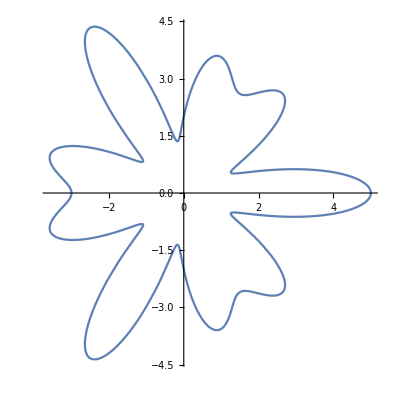

```mathematica
ParametricPlot[{Cos[t],Sin[t]}(3+Cos[6t]+Cos[9t]),{t,0,2π}]
```

```mathematica
ParametricPlot3D[r=9+s Cos[v];s=(3+Cos[3v]+Cos[6v]);{{Cos[u]r,Sin[u]r,s Sin[v]}},{u,0,2Pi},{v,0,2Pi}]
```

-Graphics3D-